Collating Metrics (first run):
1. Mills Draft - Copy.nb 
2. TEMPLATE with MASSIVE HELP from Bob Nachbar

### Span of years, accounting for co-authors

```mathematica
yearsRange=MinMax[Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]]
```

{1964,2017}

### Core Graph not including disconnected sub-graphs

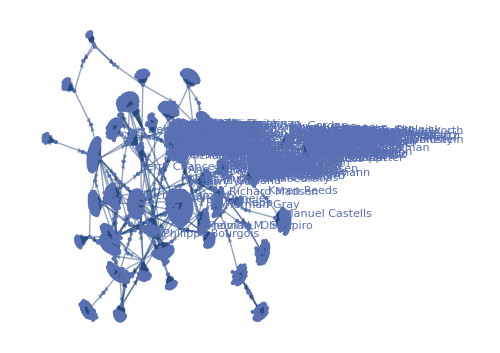

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
accumulatingGraphs=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Range@@yearsRange];
accumulatingGraphs[2017]
```

### VertexOutDegree (What is wrong with the ListPlot?)

Dataset[<>]

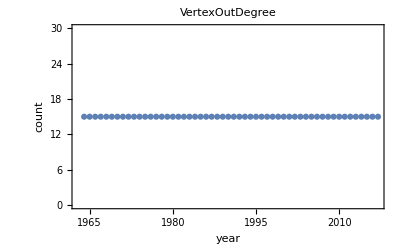

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->VertexOutDegree]
```

### VertexInDegree

Dataset[<>]

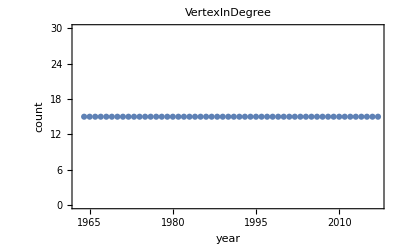

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->VertexInDegree]
```

### VertexDegree

Dataset[<>]

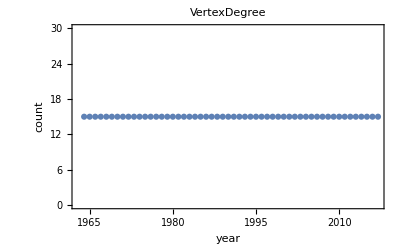

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->VertexDegree]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->VertexDegree]
```

### Closeness Centrality (WHY is this Plot Working?)

Dataset[<>]

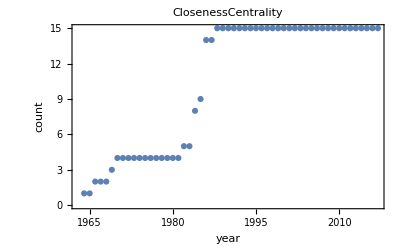

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->ClosenessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->ClosenessCentrality]
```

### EigenvectorCentrality

Dataset[<>]

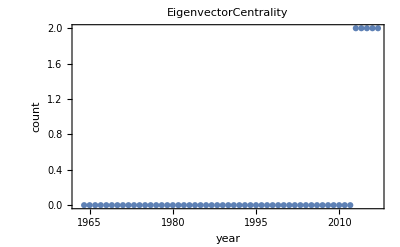

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->EigenvectorCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->EigenvectorCentrality]
```

Dataset[<>]

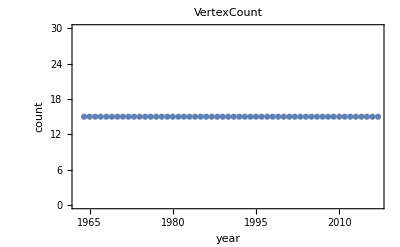

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->VertexCount]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->VertexCount]
```

Dataset[<>]

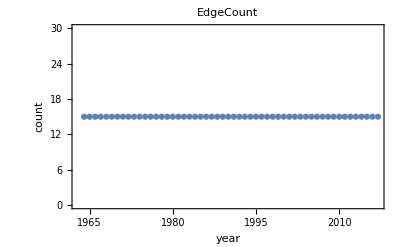

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->EdgeCount]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->EdgeCount]
```

Dataset[<>]

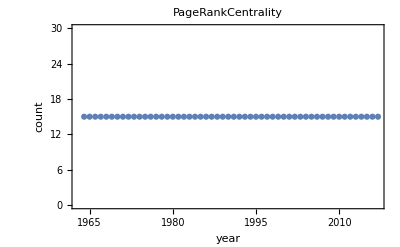

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->PageRankCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->PageRankCentrality]
```

Dataset[<>]

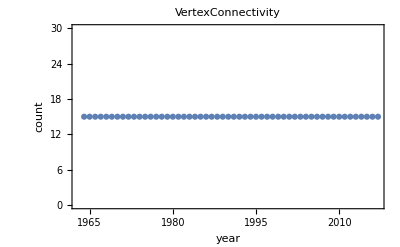

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->VertexConnectivity]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->VertexConnectivity]
```

Dataset[<>]

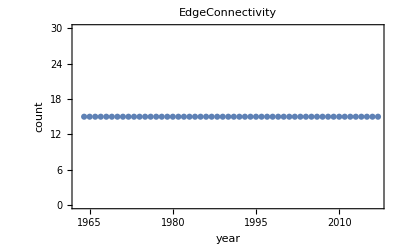

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->EdgeConnectivity]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->EdgeConnectivity]
```

Dataset[<>]

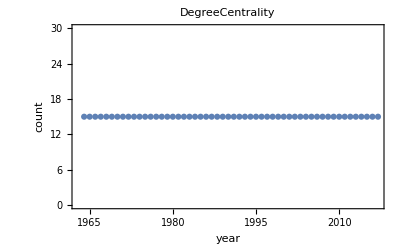

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->DegreeCentrality]
```

Dataset[<>]

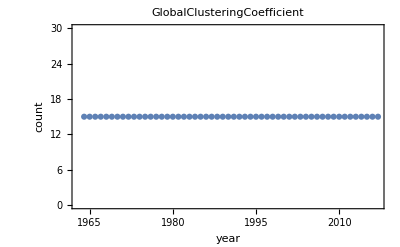

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->GlobalClusteringCoefficient]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->GlobalClusteringCoefficient]
```

Dataset[<>]

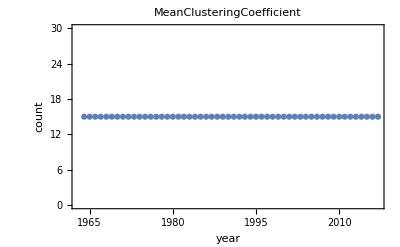

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->MeanClusteringCoefficient]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->MeanClusteringCoefficient]
```

Dataset[<>]

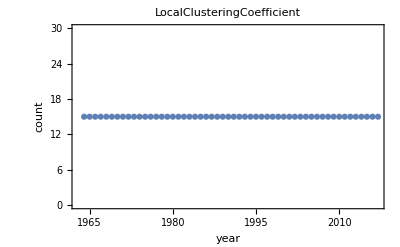

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->LocalClusteringCoefficient]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->LocalClusteringCoefficient]
```

Dataset[<>]

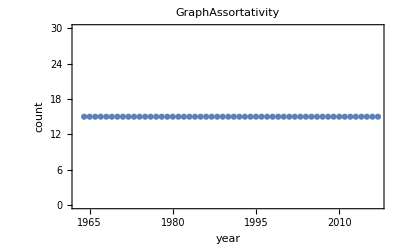

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->GraphAssortativity]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->GraphAssortativity]
```

Dataset[<>]

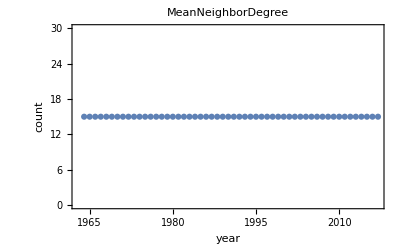

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->MeanNeighborDegree]
```

Dataset[<>]

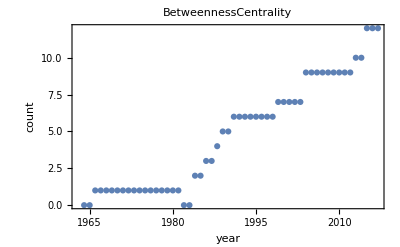

```mathematica
topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
**topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->ClosenessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsByCloseness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->ClosenessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
^^topConnectedPersonsBetweenness=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset
ListPlot[Length/@topConnectedPersonsBetweenness,FrameLabel->{"year","count"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
```

```mathematica
authorsAtPublication;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```